## Figures 1-5 for “The inherent fragility of collective proliferative control”

## Initialization Cells

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/arthurlander/Documents/RESEARCH/Manuscripts/Manuscripts_in_Progress/Mika's paper/Source Files for Mathematica Modeling

```mathematica
SP[eqnset_, xrange_, yrange_, params_]:= StreamPlot[Evaluate[eqnset/.params], xrange,yrange,RegionFunction->Function[{x0,x1},x1>=x0],RegionFillingStyle->None,RegionBoundaryStyle->None,AxesStyle->Thickness[0.0075], Frame->False, Axes->True,LabelStyle-> Large, ImageSize-> 500,StreamStyle-> Opacity[0.4], ScalingFunctions->{"Log","Log"},AspectRatio->1/GoldenRatio]
```

```mathematica
PP[system_, c0start_, c1start_, tmax_, params_]:= ParametricPlot[
Evaluate[{c0[t],c0[t]+c1[t]}/.Flatten[NDSolve[system/.params/.{c0init-> c0start, c1init-> c1start}, {c0, c1}, {t, 0, tmax}]]],{t,0,tmax},ScalingFunctions->{"Log","Log"}, PlotStyle-> {Gray,Thickness[0.015], Opacity[0.8]}, Epilog-> {PointSize[0.025],Black, Point[{Log[c0start], Log[c0start+c1start]}]}]
```

```mathematica
FixedPoints[system_, params_]:=Quiet[Simplify[{c0[t], c0[t]+c1[t]}/.Solve[system[[1;;2]]/.params/.n_'[t]-> 0, {c0[t], c1[t]}]]/.{{0,_}-> Nothing,{0.,_}-> Nothing }]
```

```mathematica
FixedPointsN[system_, params_, c0start_, c1start_]:=Simplify[{c0[t], c0[t]+c1[t]}/.FindRoot[system[[1;;2]]/.params/.n_'[t]-> 0, {{c0[t],c0start}, {c1[t],c1start}}]]
```

```mathematica
IndividualStepUp[{c0_, c1_}]:= 
With[{p=pbar/(1+(γ*c1^n1)/(1+ϕ*c0^n2))},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-k/c0) ]]}]
```

```mathematica
StepUpAsynchronous[{c0_, c1_}]:= Nest[IndividualStepUp, {c0, c1}, c0]
```

```mathematica
TotalLast[list_]:= Transpose[{First/@list, Total/@list}]
```

the following two codes are a bit faster:

```mathematica
IndividualStepUpCF = Compile[{{c0, _Integer},{c1, _Integer}, {pbar, _Real}, {n1, _Real}, {n2, _Real}, {γ, _Real}, {ϕ, _Real},{k, _Real}},
Module[{p = pbar/(1+(γ*c1^n1)/(1+ϕ*c0^n2))},{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-k/c0) ]]}],RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
StepUpAsynchronousCF = 
Compile[{{c0, _Integer},{c1, _Integer}, {pbar, _Real}, {n1, _Real}, {n2, _Real}, {γ, _Real}, {ϕ, _Real},{k, _Real}},
x0=c0; x1=c1;
Do[Module[{p = pbar/(1+(γ*x1^n1)/(1+ϕ*x0^n2))},
{x0, x1}={x0-1, x1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[IntegerPart[x1],1-ⅇ^(-k/x0) ]]}],
{c0}];
{x0, x1},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
StepUpAsynchronousCF2= 
Compile[{{c0, _Integer},{c1, _Integer}, {pbar, _Real}, {n1, _Real}, {n2, _Real}, {γ, _Real}, {ϕ, _Real},{k, _Real}},
x0=c0; x1=c1;
Do[Module[{p = pbar/(1+(γ*x1^n1)/(1+ϕ*x1^n2))},
{x0, x1}={x0-1, x1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[IntegerPart[x1],1-ⅇ^(-k/x0) ]]}],
{c0}];
{x0, x1},RuntimeAttributes->{Listable},Parallelization->True]
```

CompiledFunction[…]

```mathematica
P1[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= (2pbar)/(σ^2(c0+c1))NIntegrate[(r*k)/(k+(c1/(c0+c1))(1-(σ √(c0+c1))/λ*BesselI[0,r/λ]*BesselK[1,(σ √(c0+c1))/λ])),{r,0,σ √(c0+c1)}]
```

```mathematica
P2[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= pbar/(c0 π σ^2)NIntegrate[(r*k)/(k+((σ √c1)/λ*BesselI[1,(σ √c1)/λ]*BesselK[0,r/λ])), {r,σ √c1, σ √(c0+c1) }]
```

```mathematica
P3[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= pbar/(c0 π σ^2)NIntegrate[k/(k+(σ/λ BesselI[0,r/λ] (√c0 BesselK[1,(√c0 σ)/λ]-√(c0+c1) BesselK[1,(√(c0+c1) σ)/λ]))), {r,0, σ √c0 }]
```

```mathematica
IndividualStepUpP1[{c0_, c1_}, params_]:= 
With[{p=P1[c0, c1, k/.params, λ/.params, σ/.params, pbar/.params]},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-δ/c0) /.params]]}]
```

```mathematica
StepUpAsynchronousP1[{c0_, c1_}, params_]:= Nest[IndividualStepUpP1[#, params]&, {c0, c1}, c0]
```

```mathematica
IndividualStepUpP2[{c0_, c1_}, params_]:= 
With[{p=P2[c0, c1, k/.params, λ/.params, σ/.params, pbar/.params]},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-δ/c0) /.params]]}]
```

```mathematica
StepUpAsynchronousP2[{c0_, c1_}, params_]:= Nest[IndividualStepUpP2[#, params]&, {c0, c1}, c0]
```

```mathematica
IndividualStepUpP3[{c0_, c1_}, params_]:= 
With[{p=P3[c0, c1, k/.params, λ/.params, σ/.params, pbar/.params]},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-δ/c0) /.params]]}]
```

```mathematica
StepUpAsynchronousP3[{c0_, c1_}, params_]:= Nest[IndividualStepUpP3[#, params]&, {c0, c1}, c0]
```

## General equations for non-spatial models (Fig 1, Fig. 2A-H, Fig. 5)

```mathematica
system1 =  {c0'[t]==c0[t](2*(pbar/(1+γ*c1[t]^n1))-1),c1'[t]==2*c0[t](1-(pbar/(1+γ*c1[t]^n1)))-d*c1[t],c0[0]==c0init,c1[0]==c1init};
```

System 2 is the mixed feedback case in which diving cells inhibit the inhibition from terminal cells

```mathematica
system1a =Simplify[Flatten[Solve[system1[[1;;2]]/.{c1[t]-> s[t]-c0[t],c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+(2 pbar)/(1+γ (-c0[t]+s[t])^n1)),s'[t]==(1+d) c0[t]-d s[t]}

```mathematica
system2 = {c0'[t]==c0[t](2*(pbar/(1+(γ*c1[t]^n1)/(1+ϕ c0[t]^n2)))-1),c1'[t]==2*c0[t](1-(pbar/(1+(γ*c1[t]^n1)/(1+ϕ c0[t]^n2))))-d*c1[t],c0[0]==c0init,c1[0]==c1init};
```

```mathematica
system2a =Simplify[Flatten[Solve[system2[[1;;2]]/.{c1[t]-> s[t]-c0[t],c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+(2 pbar)/(1+(γ (-c0[t]+s[t])^n1)/(1+ϕ c0[t]^n2))),s'[t]==(1+d) c0[t]-d s[t]}

System 4 is the mixed feedback case in which terminal cells inhibit their own inhibition

```mathematica
system4 = {c0'[t]==c0[t](2*(pbar/(1+(γ*c1[t]^n1)/(1+ϕ c1[t]^n2)))-1),c1'[t]==2*c0[t](1-(pbar/(1+(γ*c1[t]^n1)/(1+ϕ c1[t]^n2))))-d*c1[t],c0[0]==c0init,c1[0]==c1init};
```

```mathematica
system4a =Simplify[Flatten[Solve[system4[[1;;2]]/.{c1[t]-> s[t]-c0[t],c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+(2 pbar)/(1+(γ (-c0[t]+s[t])^n1)/(1+ϕ (-c0[t]+s[t])^n2))),s'[t]==(1+d) c0[t]-d s[t]}

#### What is the ratio of stem to terminal cells at steady state? It is just k, the death rate constant, except when there’s fate control.

```mathematica
Solve[system2[[1;;2]]/.{n_'[t]-> 0,n1-> 1,n2-> 1}/.{c0[t]-> c0ss, c1[t]-> c1ss}, {c0ss, c1ss}]
```

{{c0ss→0,c1ss→0},{c0ss→(d-2 d pbar)/(-γ-d ϕ+2 d pbar ϕ),c1ss→(1-2 pbar)/(-γ-d ϕ+2 d pbar ϕ)}}

```mathematica
Simplify[c0ss/c1ss/.Last[%]]
```

d

```mathematica
Solve[system2[[1;;2]]/.{n_'[t]-> 0,n1-> 1,n2-> 2}/.{c0[t]-> c0ss, c1[t]-> c1ss}, {c0ss, c1ss}]
```

{{c0ss→0,c1ss→0},{c0ss→(γ-√(γ^2-4 d^2 ϕ+16 d^2 pbar ϕ-16 d^2 pbar^2 ϕ))/(2 (-d ϕ+2 d pbar ϕ)),c1ss→(γ/(-d ϕ+2 d pbar ϕ)-(√(γ^2-4 d^2 ϕ+16 d^2 pbar ϕ-16 d^2 pbar^2 ϕ))/(-d ϕ+2 d pbar ϕ))/(2 d)},{c0ss→(γ+√(γ^2-4 d^2 ϕ+16 d^2 pbar ϕ-16 d^2 pbar^2 ϕ))/(2 (-d ϕ+2 d pbar ϕ)),c1ss→(γ/(-d ϕ+2 d pbar ϕ)+(√(γ^2-4 d^2 ϕ+16 d^2 pbar ϕ-16 d^2 pbar^2 ϕ))/(-d ϕ+2 d pbar ϕ))/(2 d)}}

```mathematica
Simplify[c0ss/c1ss/.%[[2]]]
```

d

```mathematica
Solve[system2[[1;;2]]/.{n_'[t]-> 0,n1-> 2,n2-> 2}/.{c0[t]-> c0ss, c1[t]-> c1ss}, {c0ss, c1ss}]
```

{{c0ss→0,c1ss→0},{c0ss→-(√(d^2-2 d^2 pbar))/(√(-γ-d^2 ϕ+2 d^2 pbar ϕ)),c1ss→-(√(-d^2 (-1+2 pbar)))/(d √(-γ-d^2 ϕ+2 d^2 pbar ϕ))},{c0ss→(√(d^2-2 d^2 pbar))/(√(-γ-d^2 ϕ+2 d^2 pbar ϕ)),c1ss→(√(d^2-2 d^2 pbar))/(d √(-γ-d^2 ϕ+2 d^2 pbar ϕ))}}

```mathematica
Simplify[c0ss/c1ss/.%[[2]]]
```

d

## Theory and equations for “pseudo”-spatial models (Fig 2I-P; Fig 4)

Let c0 stand for dividing cells and c1 for terminal cells.  Our general functions for the growth of c0 and c1 are (in time units = cell cycle)

c0’[t] = (2p-1)c0[t],
c1’[t] = 2(1-p)c0[t] -δ c1[t]

For nonspatial models we use a Hill function formulation of p, typically:

p = pbar/(1+ (γ c1[t])^n)

where γ and n are positive constants, and pbar is a constant between 0.5 and 1.

For “pseudo” spatial models we develop this theory:

1.  The function, in radial coordinates, for the steady-state, 2-dimensional diffusion gradient within a disc of radius b, where production is uniform within the disc and zero elsewhere, and decay is uniform everywhere, may be found in Chen et al., 2016, and is:
1-(b 1b/λ 0r/λ)/λ, r<b
Where r is radial distance and λ is the decay length √(D/k) defined by diffusion coefficient D and decay rate constant k, I_ is a modified Bessel function of the first kind and K _ is a modified Bessel function of the second kind.  .   

2.  The radius of a disc with a total number of cells = χ  is found by taking the total Area dividing by π and taking the square root.  If the radius of a cell is σ, then the area of each cell is π σ^2, so the total area is χ π σ^2, therefore the radius of the disc is √((χ π σ^2)/π) = σ √χ.

If will use c1 to represent terminal cells and c0 to represent dividing cells:  Then the formula for the amount of feedback factor at any given point is 
v (1-((σ √(c0+c1)) 0r/λ 1(σ √(c0+c1))/λ)/λ)
where v is the rate of production.  If the factor is being made only by c1 cells, then the rate of production is v (c1/(c0+c1)), where v is an arbitrary constant.  
According to the formula p = pbar/(1+ F/γ), where F is the concentration of the secreted feedback factor,  the pvalue at any point r is thus:
pbar/((c1 v)/(γ (c0+c1)) (1-((σ √(c0+c1)) 0r/λ 1(σ √(c0+c1))/λ)/λ)+1)
We define k = γ/v and re-write this as
(k pbar)/(c1/(c0+c1) (1-((σ √(c0+c1)) 0r/λ 1(σ √(c0+c1))/λ)/λ)+k)

Note that k represents 1/feedback strength, i.e. the lower the k the stronger the feedback.

3. Getting the average pvalue over an entire disc
To get the average pvalue, we must integrate p over the disc, which means we multiply by 2π r and take the integral from 0 to the overall radius, σ √χ = σ √(c0+c1), and then divide by the area of the disc, which is π ( (σ Sqrt[c0 + c1]))^2.   Ultimately we get 

1/(π σ^2(c0+c1))NIntegrate[(2 π r*k* pbar)/(k+(c1/(c0+c1))(1-(σ √(c0+c1))/λ*BesselI[0,r/λ]*BesselK[1,(σ √(c0+c1))/λ])),{r,0,σ √(c0+c1)}]

pulling constants 2 π pbar out of the numerator of the integrand, we get the following formula for p

(2pbar)/(σ^2(c0+c1))∫_0^(σ √(c0+c1)) (r*k)/(k+(c1/(c0+c1))(1-(σ √(c0+c1))/λ*BesselI[0,r/λ]*BesselK[1,(σ √(c0+c1))/λ]))ⅆr

```mathematica
P[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= (2pbar)/(σ^2(c0+c1))NIntegrate[(r*k)/(k+(c1/(c0+c1))(1-(σ √(c0+c1))/λ*BesselI[0,r/λ]*BesselK[1,(σ √(c0+c1))/λ])),{r,0,σ √(c0+c1)}]
```

For spatial models in which cells sort away from each other

Here we must calculate the diffusion gradients within just the regions that contain dividing cells, and average the p value just there.

For this we will need to use the more complete equation from Chen et al., which gives the diffusion gradients both inside and outside discs that are producing a diffusible molecule.  

Inside:  1-b/λ 1b/λ 0r/λ
Outside:  b/λ 1b/λ 0r/λ

Case 1:  Dividing cells are on the outside of the disc and terminal cells are on the inside.  We this have two radii to deal with, b1 is the radius of the disc formed by terminal cells, b2 is the radius of the entire disc.  We note that b1 = σ √c1, whereas b2 = σ √(c0+c1)

In this case, the gradient we need to average over is an outside gradient from b1 (and all the cells are producing in it), and we need to average p from b1 to b2.  Thus the p value at any point r, (between b1 and b2) is 
(k pbar)/(b1/λ 1b1/λ 0r/λ+k) ->(k pbar)/(((√c1 σ)/λ) 0r/λ 1(σ √c1)/λ+k)

So we need to integrate this, multiplied by 2πr,  from r=b1 to r=b2, and then divide by the area of the annulus between b1 and b2, which is π b2^2-π b1^2 = 
π (σ^2(c0+c1) - σ^2 c1) = c0 π σ^2.  Pulling out pbar gives us:

pbar/(c0 π σ^2)∫_(σ √c1)^(σ √(c0+c1)) (2 π k r)/(k+((σ √c1)/λ*BesselI[1,(σ √c1)/λ]*BesselK[0,r/λ]))ⅆr

```mathematica
P2[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= (2pbar)/(c0 σ^2)NIntegrate[(r*k)/(k+((σ √c1)/λ*BesselI[1,(σ √c1)/λ]*BesselK[0,r/λ])), {r,σ √c1, σ √(c0+c1) }]
```

Case 2 : Dividing cells are on the inside of the disc and terminal cells are on the outside.  We this have two radii to deal with, b1 is the radius of the disc formed by dividing cells, b2 is the radius of the entire disc.  We note that b1 = σ √c0, whereas b2 = σ √(c0+c1)

In this case, the gradient we need to average over is an inside gradient, which we obtain by first finding the inside gradient assuming all cells are c1 all the way out to b2, and then subtract the inside gradient we obtain when all cells are c1 going all the way out to b1.  We then average this gradient over the disc with radius b1.

The first gradient is thus  1- b2/λ BesselI[0,r/λ] BesselK[1,b2/λ] and the gradient we subtract from it is 1- b1/λ BesselI[0,r/λ] BesselK[1,b1/λ].  Thus the true gradient is:

```mathematica
Simplify[1-b2/λ 1b2/λ 0r/λ-(1-b1/λ 1b1/λ 0r/λ)/.{b1->σ √c0, b2-> σ √(c0+c1)}] which gives us:
```

```mathematica
0r/λ ((σ √c0)/λ 1(√c0 σ)/λ-(σ √(c0+c1))/λ 1(σ √(c0+c1))/λ)
```

which means the pvalue is   (k pbar)/(k+  0r/λ ((σ √c0)/λ 1(√c0 σ)/λ-(σ √(c0+c1))/λ 1(σ √(c0+c1))/λ))
So we need to integrate this, multiplied by 2πr,  from r=0 to r=b1, and then divide by the area of π b1^2 = π σ^2c0.  Pulling out the pbar gives us:

pbar/(c0 π σ^2)∫_0^(σ √c0) (2 π r k)/(k+(σ/λ BesselI[0,r/λ] (√c0 BesselK[1,(√c0 σ)/λ]-√(c0+c1) BesselK[1,(√(c0+c1) σ)/λ])))ⅆr

```mathematica
P3[c0_?NumericQ,c1_?NumericQ,k_,λ_,σ_, pbar_]:= (2 pbar)/(c0  σ^2)NIntegrate[(r*k)/(k+(σ/λ BesselI[0,r/λ] (√c0 BesselK[1,(√c0 σ)/λ]-√(c0+c1) BesselK[1,(√(c0+c1) σ)/λ]))), {r,0, σ √c0 }]
```

```mathematica
systemA={c0'[t] == (2*P1[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P1[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

```mathematica
systemAa=Simplify[Flatten[Solve[systemA[[1;;2]]/.{c1[t]-> s[t]-c0[t], c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+2 P1[c0[t],-c0[t]+s[t],k,λ,σ,pbar]),s'[t]==(1+δ) c0[t]-δ s[t]}

```mathematica
systemB={c0'[t] == (2*P2[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P2[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

```mathematica
systemBa=Simplify[Flatten[Solve[systemB[[1;;2]]/.{c1[t]-> s[t]-c0[t], c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+2 P2[c0[t],-c0[t]+s[t],k,λ,σ,pbar]),s'[t]==(1+δ) c0[t]-δ s[t]}

```mathematica
systemC={c0'[t] == (2*P3[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P3[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

```mathematica
systemCa=Simplify[Flatten[Solve[systemC[[1;;2]]/.{c1[t]-> s[t]-c0[t], c1'[t]-> s'[t]-c0'[t]}, {c0'[t], s'[t]}]]]/.Rule-> Equal
```

{c0'[t]==c0[t] (-1+2 P3[c0[t],-c0[t]+s[t],k,λ,σ,pbar]),s'[t]==(1+δ) c0[t]-δ s[t]}

## Figure 1A,B

### Without feedback (Fig. 1A)

Here we choose assymmetry by allowing every daughter to differentiate independently

```mathematica
StepUpNew[{z_, w_}]:= With[{x=RandomVariate[BinomialDistribution[2z,0.5]]}, {x, w+2z-x-RandomVariate[BinomialDistribution[w,0.5]]}]
```

```mathematica
StepUpNew[{500,1000}]
```

{520,984}

Here are two examples. The first was used as Figure 1a

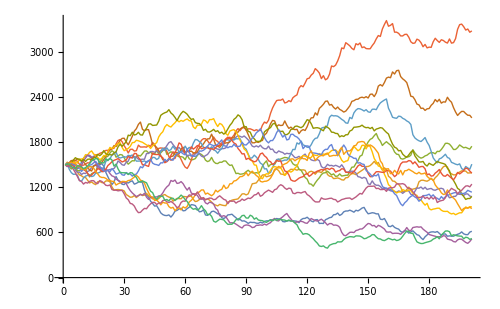

```mathematica
ListPlot[Table[Total/@NestList[StepUpNew, {500,1000}, 200], {15}], PlotStyle-> Thick,Joined-> True, ImageSize-> 500, LabelStyle-> {Black, Large}, AxesStyle-> Thick]
```

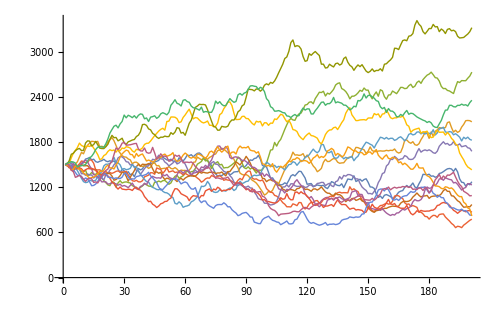

```mathematica
ListPlot[Table[Total/@NestList[StepUpNew, {500,1000}, 200], {15}], PlotStyle-> Thick,Joined-> True, ImageSize-> 500, LabelStyle-> {Black, Large}, AxesStyle-> Thick]
```

### With feedback (Fig. 1B)

```mathematica
stochSim=Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF[#1, #2,1,1, 0,0.001, 0,0.5]&,#]&, {500,1000}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 200]], {100}]],1];
```

```mathematica
Dimensions[stochSim]
```

{100,201,2}

```mathematica
ListPlot[Map[Last, stochSim, {2}], PlotStyle-> Thick,Joined-> True, ImageSize-> 500, LabelStyle-> {Black, Large}, AxesStyle-> Thick, PlotRange-> {0, 3500}]
```

```mathematica
Export["stochSim.mx", stochSim]
```

stochSim.mx

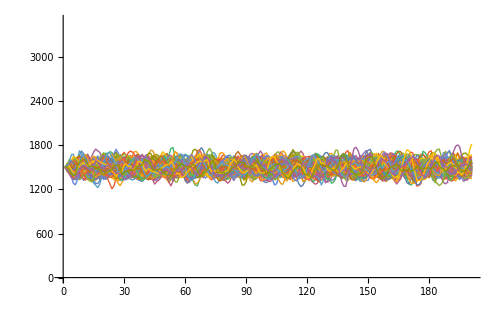

```mathematica
ListPlot[Map[Last, stochSim, {2}], PlotStyle-> Thick,Joined-> True, ImageSize-> 500, LabelStyle-> {Black, Large}, AxesStyle-> Thick, PlotRange-> {0, 3500}]
```

The following is a random sample of 15 trajectories and was used for Figure 1B

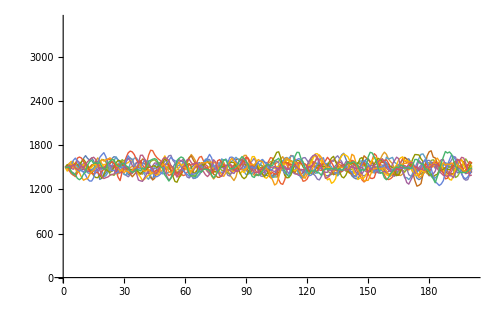

```mathematica
ListPlot[RandomSample[Map[Last, stochSim, {2}],15], PlotStyle-> Thick,Joined-> True, ImageSize-> 500, LabelStyle-> {Black, Large}, AxesStyle-> Thick, PlotRange-> {0, 3500}]
```

## Figure 2B,C,D (non-spatial, steady state)

### Fig. 2B

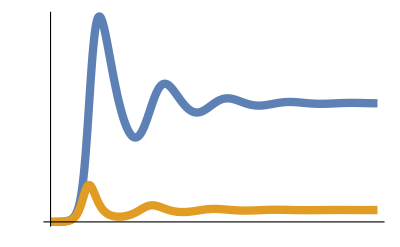

```mathematica
Block[{n1=1,  γ=0.000045, c0init=1, c1init=0, tmax=200, pbar=0.7, d=0.1}, 
With[{solset=Flatten@NDSolve[system1, {c0, c1}, {t, 0, tmax}]},
Plot[Evaluate[{c1[t],c0[t]}/.solset],{t,0,tmax},PlotStyle -> Thickness[0.015],AxesStyle->Thick,Ticks->{{#,"",{0.0,0.025}}&/@Range[0,200,50],{#,"",{0.0,0.025}}&/@Range[0,20000,5000]}]]]
```

### Fig. 2C

```mathematica
params7= {n1-> 1, γ->0.000045, pbar->0.7,d->0.1};
```

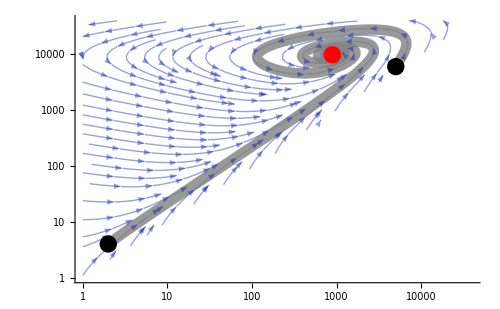

```mathematica
fig2calt5alt=
With[{terms=Last/@system1a/.n_[t]-> n},With[{system=system1,c0init1=2, c1init1=2, c0init2=5000, c1init2=1000,tmax=500, params=params7},Show[SP[terms, {c0,1,4 10^4},{s,1,4 10^4},params],PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red, Point[Log[#]]}&/@FixedPoints[system, params]}]]]
```

### Fig. 2D

```mathematica
stochSim2alt=Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF[#1, #2,pbar/.params7,n1/.params7, 0, γ/.params7, 0, d/.params7]&,#]&, {1,0}, 10^4>First[#]>0&, 2, 100]], {100}]],1];
```

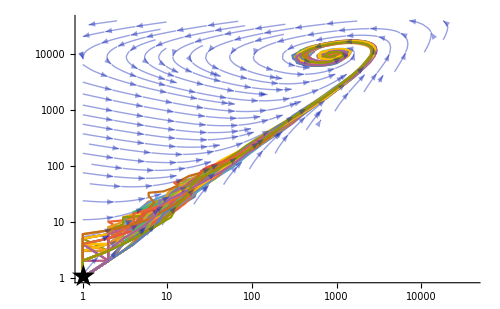

```mathematica
fig2dalt=With[{terms=Last/@system1a/.n_[t]-> n},Show[SP[terms, {c0,1,4 10^4},{s,1,4 10^4},params7],ListLogLogPlot[stochSim2alt, Joined-> True],Epilog-> Inset[Style["\[FivePointedStar]",30, Black], Log@{1,1}]]]
```

```mathematica
Export["fig2dalt.mx", stochSim2alt]
```

fig2dalt.mx

## Figure 2F,G,H (non-spatial, steady state)

### Fig . 2F

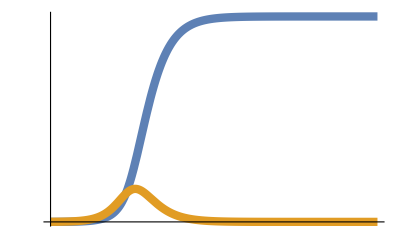

```mathematica
Block[{n1=1,  γ=0.001, c0init=1, c1init=0, tmax=40, pbar=0.85, d=0}, 
With[{solset=Flatten@NDSolve[system1, {c0, c1}, {t, 0, tmax}]},
Plot[Evaluate[{c1[t],c0[t]}/.solset],{t,0,40},PlotStyle -> Thickness[0.015],AxesStyle->Thick,Ticks->{{#,"",{0.0,0.025}}&/@Range[0,40,10],{#,"",{0.0,0.025}}&/@Range[0,2500,500]}]]]
```

### Fig . 2G

```mathematica
params1= {n1-> 1, γ->0.001, pbar->0.85,d->0};
```

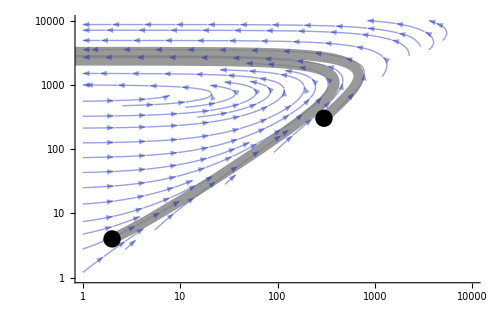

```mathematica
fig2g=With[{terms=Last/@system1a/.n_[t]-> n},With[{system=system1, c0init1=2, c1init1=2, c0init2=300, c1init2=2,tmax=500, params=params1},
Show[SP[terms, {c0,1,10^4},{s,1,10^4}, params],PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red, Point[#]}&/@FixedPoints[system, params]}]]]
```

### Fig . 2H

```mathematica
stochSim1=Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF[#1, #2,pbar/.params1,n1/.params1, 0, γ/.params1, 0, d/.params1]&,#]&, {1,0}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 100]], {100}]],1];
```

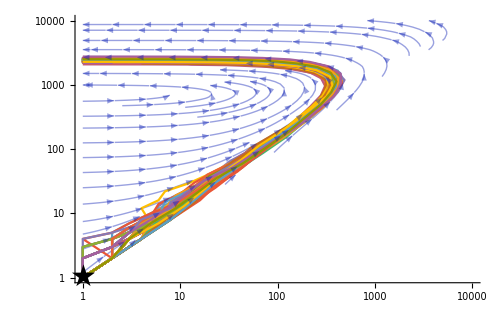

```mathematica
fig2h=With[{terms=Last/@system1a/.n_[t]-> n},Show[SP[terms, {c0,1,10^4},{s,1,10^4}, params1],ListLogLogPlot[stochSim1, Joined-> True],Epilog-> Inset[Style["\[FivePointedStar]",30, Black], Log@{1,1}]]]
```

```mathematica
Export["fig2h.mx", stochSim1]
```

fig2h.mx

## Figure 2 J, J’, N, N’ (Spatial models, well mixed, time plots)

```mathematica
systemA={c0'[t] == (2*P1[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P1[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

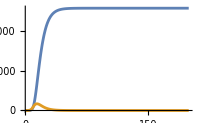

```mathematica
fig2N=
Block[{k=0.75, λ=100, σ=5, pbar=0.9, c0init=1, c1init=0, tend=200, δ=0},
With[{solset= Flatten[NDSolve[systemA, {c0, c1}, {t, 0, tend}]]},
Plot[Evaluate[{c1[t], c0[t]}/.solset], {t, 0, tend}, PlotStyle-> Thickness[0.01], ImageSize-> 200, LabelStyle-> Medium]]]
```

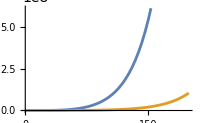

```mathematica
fig2Nprime=
Block[{k=1.3, λ=100, σ=5, pbar=0.9, c0init=1, c1init=0, tend=200, δ=0},
With[{solset= Flatten[NDSolve[systemA, {c0, c1}, {t, 0, tend}]]},
Plot[Evaluate[{c1[t], c0[t]}/.solset], {t, 0, tend}, PlotStyle-> Thickness[0.01], ImageSize-> 200, LabelStyle-> Medium]]]
```

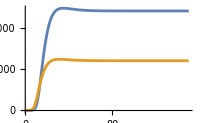

```mathematica
fig2J=
Block[{k=0.7, λ=100, σ=5, pbar=0.9, c0init=1, c1init=0, tend=150, δ=0.5},
With[{solset= Flatten[NDSolve[systemA, {c0, c1}, {t, 0, tend}]]},
Plot[Evaluate[{c1[t], c0[t]}/.solset], {t, 0, tend}, PlotStyle-> Thickness[0.01], ImageSize-> 200, LabelStyle-> Medium]]
]
```

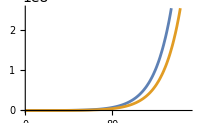

```mathematica
fig2Jprime=
Block[{k=0.9, λ=100, σ=5, pbar=0.9, c0init=1, c1init=0, tend=150, δ=0.5},
With[{solset= Flatten[NDSolve[systemA, {c0, c1}, {t, 0, tend}]]},
Plot[Evaluate[{c1[t], c0[t]}/.solset], {t, 0, tend}, PlotStyle-> Thickness[0.01], ImageSize-> 200, LabelStyle-> Medium]]
]
```

## Figure 2 K, O (Spatial models, well mixed, Stream Plots)

#### Figure 2K

```mathematica
params8={k->0.5, λ-> 100, σ-> 5, pbar-> 0.9, tend-> 200, δ-> 0.1};
```

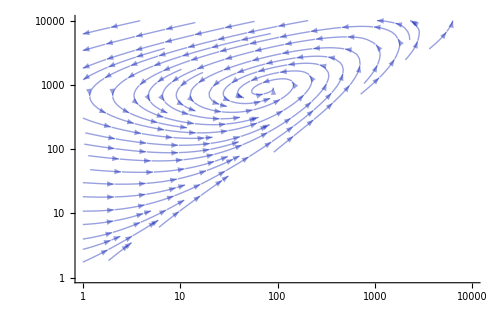

```mathematica
stream3=With[{terms=Last/@systemAa/.n_[t]-> n},SP[terms, {c0,1,10^4},{s,1,10^4}, params8]]
```

```mathematica
fp8=FixedPointsN[systemA, params8, 90,900]
```

{77.4103,851.513}

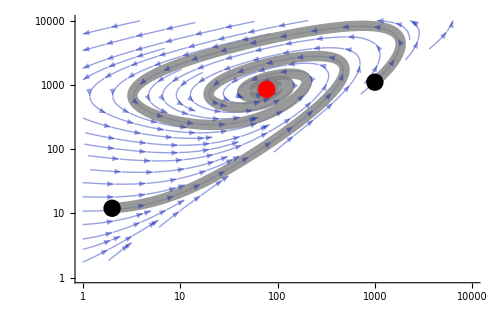

```mathematica
With[{system=systemA, c0init1=2, c1init1=10, c0init2=1000, c1init2=100,tmax=500, params=params8},
Show[stream3,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red, Point[Log@fp8]}}]]
```

#### Figure 2O

```mathematica
params9={k->0.5, λ-> 100, σ-> 5, pbar-> 0.9, tend-> 200, δ->0};
```

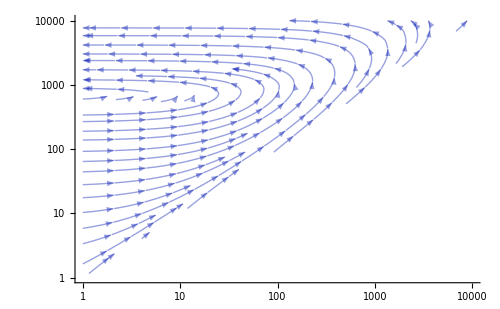

```mathematica
stream4=With[{terms=Last/@systemAa/.n_[t]-> n},SP[terms, {c0,1,10^4},{s,1,10^4}, params9]]
```

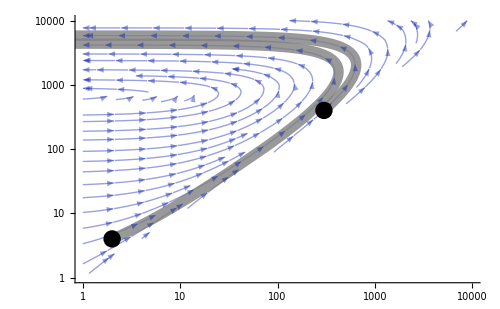

```mathematica
With[{system=systemA, c0init1=2, c1init1=2, c0init2=300, c1init2=100,tmax=500, params=params9},
Show[stream4,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] }]]
```

## Figure 2 L, P (Spatial models, well mixed, stochastic simulations)

```mathematica
IndividualStepUpP1[{c0_, c1_}, params_]:= 
With[{p=P1[c0, c1, k/.params, λ/.params, σ/.params, pbar/.params]},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-δ/c0) /.params]]}]
```

```mathematica
StepUpAsynchronousP1[{c0_, c1_}, params_]:= Nest[IndividualStepUpP1[#, params]&, {c0, c1}, c0]
```

#### Figure 2P

```mathematica
params9
```

{k→0.5,λ→100,σ→5,pbar→0.9,tend→200,δ→0}

```mathematica
AbsoluteTiming[
stochSim4=Flatten[Last@
Reap[
Do[Sow[TotalLast@NestWhileList[StepUpAsynchronousP1[#, params9]&, {20,20}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 100]], {50}]],1];]
```

{342.716,Null}

```mathematica
Export["stochSim4.mx",stochSim4]
```

stochSim4.mx

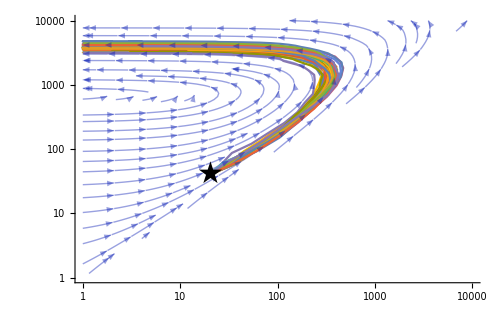

```mathematica
Show[stream4,ListLogLogPlot[stochSim4, Joined-> True],Epilog->  Inset[Style["\[FivePointedStar]",30, Black], Log@{20,40}]]
```

#### Figure 2L

```mathematica
params8
```

{k→0.5,λ→100,σ→5,pbar→0.9,tend→200,δ→0.1}

```mathematica
AbsoluteTiming[
stochSim3=Flatten[Last@
Reap[
Do[Sow[TotalLast@NestWhileList[StepUpAsynchronousP1[#, params8]&, {10,10}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 100]], {50}]],1];]
```

{918.564,Null}

```mathematica
Export["stochSim3.mx",stochSim3]
```

stochSim3.mx

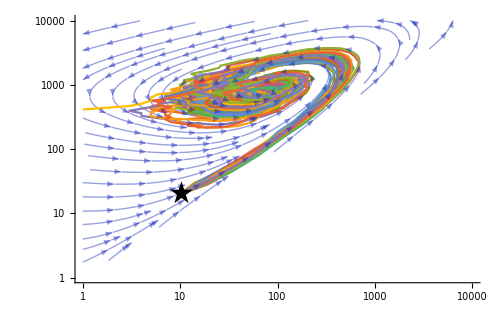

```mathematica
Show[stream3,ListLogLogPlot[stochSim3, Joined-> True],Epilog->  Inset[Style["\[FivePointedStar]",30, Black], Log@{10,20}]]
```

## Figure 3 C, D (Agent based simulation, final-state system)

### Initialization Cells

The following code is required to replicate what is in Figure 3C-D

#### Functions

BoolEval is code from Szabolcs Horvát and is available at https : // github . com/szhorvat/BoolEval

```mathematica
<<BoolEval`
```

```mathematica
CreateBaseTable[λ_]:= 
With[{ulq=Chop[ 1/(2λ) BesselI[1,1/(2λ)] *Table[N@BesselK[0,(√((x-801)^2+(y-801)^2))/λ], {x, 1, 800}, {y,1, 800}]],
leftrow=Chop[N@Table[ 1/(2λ) BesselI[1,1/(2λ)] BesselK[0,(√((y-801)^2))/λ], {y, 1, 800}]]},
SparseArray[Join[
Transpose[Join[ulq, {leftrow}, Reverse[ulq]]], {Join[leftrow, {0}, Reverse[leftrow]]},Reverse[Transpose[Join[ulq, {leftrow}, Reverse[ulq]]]]],{1601, 1601}]]
```

```mathematica
LabeledArray[array_, cases_]:= Table[{i,1}-> array, {i, cases}]
```

```mathematica
MaxPossible[λ_]:=(3.514 λ^2)/(1+4.581 λ^2)
```

```mathematica
CreateOrganizedList3[labeledarray_,basetable_, iterations_, λ_, γ_, n_, p0_]:=
Module[{f=GrowthSimulation3[#,basetable,λ,γ, n, p0]& , step, steplist},
step=Flatten[labeledarray];
steplist={step};
Do[step=Thread[(Plus[#,{0,1}]&/@Keys[step])-> (f/@Values[step])];
AppendTo[steplist, step];
Print[i, Now," still dividing = ", Total[(BoolEval[#==1]["ExplicitLength"])&/@Values[step]]],{i,iterations}];
Print["done"];
steplist]
```

```mathematica
DiffusionMap[basetable_, points_]:= Total[Take[basetable,{802-#[[1]], 1602-#[[1]]},{802-#[[2]], 1602-#[[2]]}]&/@points]
```

```mathematica
Options[GrowthSimulation3]={"Max Size"-> 75000};

GrowthSimulation3[array_,basetable_,λ_,  γ_, n_, p0_, OptionsPattern[]]:=
Module[{bounds, searchspace,div, diff, divs, diffs, diffusionfield,newarray, donor,recipient, elementlist, neighbormatrix,i, shovedmat},
div=SparseArray[BoolEval[array> 0]];
diff= SparseArray[BoolEval[array== -1]];
If[0<div["ExplicitLength"]<OptionValue["Max Size"],
diffusionfield=DiffusionMap[basetable, diff["ExplicitPositions"]];
newarray=
SparseArray[Join[
Thread[RandomSample[div["ExplicitPositions"]] -> N[Range[div["ExplicitLength"]]]],
Thread[diff["ExplicitPositions"] -> Table[-1, diff["ExplicitLength"]]],
{{_,_}-> 0}],Dimensions[array]];
elementlist=
Map[Apply[diffusionfield[[##]]&,#]&, N[Range[div["ExplicitLength"]]]/.(Reverse/@ArrayRules[newarray])];
For[i=1, i<= div["ExplicitLength"],i++,
divs=SparseArray[BoolEval[newarray> 0]]["ExplicitPositions"];
diffs=SparseArray[BoolEval[newarray==-1]]["ExplicitPositions"];
bounds=Flatten[MinMax[Union[#]]+{-1,1}&/@Transpose[Join[divs, diffs]]]; searchspace=Complement[Flatten[Table[{x, y}, {x, bounds[[1]], bounds[[2]]}, {y, bounds[[3]], bounds[[4]]}],1],newarray["ExplicitPositions"]];
donor=N[i]/.Reverse/@ArrayRules[newarray];
recipient= RandomChoice[Nearest[searchspace,donor]];
newarray=SparseArray[JustShoveCF[Normal[newarray],elementlist[[i]],donor, recipient]]];
Map[ChooseFate2[#, γ, n, p0]&,newarray, {2}],
array]]
```

```mathematica
JustShoveCF=Compile[{{matrix, _Real, 2},{element, _Real},{donor, _Integer, 1},{recipient, _Integer, 1}},
Which[donor⟦1⟧==recipient⟦1⟧,
PushHorizontalCF[matrix,element,donor,recipient],
donor⟦2⟧==recipient⟦2⟧,
PushVerticalCF[matrix,element,donor,recipient],
RandomInteger[]==1,PushMixedACF[matrix,element,donor,recipient],
True,PushMixedBCF[matrix,element,donor,recipient]], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
ChooseFate2[x_, γ_, n_, p0_]:= Which[x==-1, -1,x==0, 0,True, With[{p=p0/(1+( x/γ)^n)},RandomChoice[{p,1-p}-> {1,-1}]]]
```

```mathematica
PushHorizontalCF=Compile[{{matrix, _Real, 2},{element, _Real},{donor, _Integer, 1},{recipient, _Integer, 1}},
Module[{row,newrow,x1,y1,x2,y2},
x1=donor⟦1⟧;y1=donor⟦2⟧;x2=recipient⟦1⟧;y2=recipient⟦2⟧;
row=matrix⟦x1⟧;
newrow=
If[y2>y1,
Join[row⟦1;;y1-1⟧,{element,element},Which[y2>y1+2,row⟦y1+1;;y2-1⟧,y2>y1+1,{row⟦y1+1⟧},True,{}],row⟦y2+1;;Length[row]⟧],Join[row⟦1;;y2-1⟧,Which[y1>y2+2,row⟦y2+1;;y1-1⟧,y1>y2+1,{row⟦y2+1⟧},True,{}],{element,element},row⟦y1+1;;Length[row]⟧]];Join[matrix⟦1;;x1-1⟧,{newrow},matrix⟦x1+1;;Length[Transpose[matrix]]⟧]],
RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
PushVerticalCF=Compile[{{matrix, _Real, 2},{element, _Real},{donor, _Integer, 1},{recipient, _Integer, 1}},Module[{matT,row,newrow,donorT,recipientT,x1,y1,x2,y2},
matT=Transpose[matrix];x1=donor⟦2⟧; y1=donor⟦1⟧; x2=recipient⟦2⟧; y2=recipient⟦1⟧;row=matT⟦x1⟧;
newrow=
If[y2>y1,
Join[row⟦1;;y1-1⟧,{element,element},Which[y2>y1+2,row⟦y1+1;;y2-1⟧,y2>y1+1,{row⟦y1+1⟧},True,{}],row⟦y2+1;;Length[row]⟧],Join[row⟦1;;y2-1⟧,Which[y1>y2+2,row⟦y2+1;;y1-1⟧,y1>y2+1,{row⟦y2+1⟧},True,{}],{element,element},row⟦y1+1;;Length[row]⟧]];Transpose[Join[matT⟦1;;x1-1⟧,{newrow},matT⟦x1+1;;Length[matrix]⟧]]],
RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
PushMixedACF=Compile[{{matrix, _Real, 2},{element, _Real},{donor, _Integer, 1},{recipient, _Integer, 1}},
Module[{matT,mat,row,newrow,donorT,recipientT,x1,y1,x2,y2},
matT=Transpose[matrix];x1=recipient⟦2⟧;y1=donor⟦1⟧;x2=recipient⟦2⟧;y2=recipient⟦1⟧;row=matT⟦x1⟧;newrow=If[y2>y1,
Join[row⟦1;;y1-1⟧,{0},row⟦y1;;y2-1⟧,row⟦y2+1;;Length[row]⟧],Join[row⟦1;;y2-1⟧,row⟦y2+1;;y1⟧,{0},row⟦y1+1;;Length[row]⟧]];mat=Transpose[Join[matT⟦1;;x1-1⟧,{newrow},matT⟦x1+1;;Length[matrix]⟧]];x1=donor⟦1⟧;y1=donor⟦2⟧;x2=donor⟦1⟧;y2=recipient⟦2⟧;row=mat⟦x1⟧;newrow=
If[y2>y1,
Join[row⟦1;;y1-1⟧,{element,element},Which[y2>y1+2,row⟦y1+1;;y2-1⟧,y2>y1+1,{row⟦y1+1⟧},True,{}],row⟦y2+1;;Length[row]⟧],Join[row⟦1;;y2-1⟧,Which[y1>y2+2,row⟦y2+1;;y1-1⟧,y1>y2+1,{row⟦y2+1⟧},True,{}],{element,element},row⟦y1+1;;Length[row]⟧]];Join[mat⟦1;;x1-1⟧,{newrow},mat⟦x1+1;;Length[matT]⟧]],
RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
PushMixedBCF=Compile[{{matrix, _Real, 2},{element, _Real},{donor, _Integer, 1},{recipient, _Integer, 1}},
Module[{matT,mat,row,newrow,donorT,recipientT,x1,y1,x2,y2},
x1=recipient⟦1⟧;y1=donor⟦2⟧;x2=recipient⟦1⟧;y2=recipient⟦2⟧;row=matrix⟦x1⟧;
newrow=If[y2>y1,
Join[row⟦1;;y1-1⟧,{0},row⟦y1;;y2-1⟧,row⟦y2+1;;Length[row]⟧],
Join[row⟦1;;y2-1⟧,row⟦y2+1;;y1⟧,{0},row⟦y1+1;;Length[row]⟧]];matT=Transpose[Join[matrix⟦1;;x1-1⟧,{newrow},matrix⟦x1+1;;Length[Transpose[matrix]]⟧]];x1=donor⟦2⟧;y1=donor⟦1⟧;x2=donor⟦2⟧;y2=recipient⟦1⟧;row=matT⟦x1⟧;
newrow=If[y2>y1,
Join[row⟦1;;y1-1⟧,{element,element},Which[y2>y1+2,row⟦y1+1;;y2-1⟧,y2>y1+1,{row⟦y1+1⟧},True,{}],row⟦y2+1;;Length[row]⟧],Join[row⟦1;;y2-1⟧,Which[y1>y2+2,row⟦y2+1;;y1-1⟧,y1>y2+1,{row⟦y2+1⟧},True,{}],{element,element},row⟦y1+1;;Length[row]⟧]];Transpose[Join[matT⟦1;;x1-1⟧,{newrow},matT⟦x1+1;;Length[matrix]⟧]]],
RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
CellPlot[array_, pr_]:=ArrayPlot[array, PlotRange-> {pr,pr},ImageSize-> 400,ColorFunctionScaling->False, ColorFunction-> (Which[#==1,Orange,#==-1, Blue, True, White]&), Frame-> None]
```

### Generating Data for Figure 3 C

```mathematica
la= LabeledArray[newArray1, 100];
```

```mathematica
basetable=CreateBaseTable[2];
```

```mathematica
Print[Now];simulations017a=CreateOrganizedList3[la,basetable, 30, 2, 0.14, 2, 1];
```

Tue 26 Dec 2023 06:26:27GMT-8

1Tue 26 Dec 2023 06:27:47GMT-8 still dividing = 16188

2Tue 26 Dec 2023 06:29:20GMT-8 still dividing = 25502

3Tue 26 Dec 2023 06:32:05GMT-8 still dividing = 37590

4Tue 26 Dec 2023 06:35:47GMT-8 still dividing = 48692

5Tue 26 Dec 2023 06:41:03GMT-8 still dividing = 50234

6Tue 26 Dec 2023 06:45:13GMT-8 still dividing = 37884

7Tue 26 Dec 2023 06:49:23GMT-8 still dividing = 22328

8Tue 26 Dec 2023 06:51:57GMT-8 still dividing = 12635

9Tue 26 Dec 2023 06:53:39GMT-8 still dividing = 7892

10Tue 26 Dec 2023 06:54:46GMT-8 still dividing = 5653

11Tue 26 Dec 2023 06:55:35GMT-8 still dividing = 4942

12Tue 26 Dec 2023 06:56:20GMT-8 still dividing = 5184

13Tue 26 Dec 2023 06:57:11GMT-8 still dividing = 6203

14Tue 26 Dec 2023 06:58:24GMT-8 still dividing = 8089

15Tue 26 Dec 2023 07:00:38GMT-8 still dividing = 11424

16Tue 26 Dec 2023 07:04:49GMT-8 still dividing = 16854

17Tue 26 Dec 2023 07:12:19GMT-8 still dividing = 24931

18Tue 26 Dec 2023 07:25:59GMT-8 still dividing = 35289

19Tue 26 Dec 2023 07:50:18GMT-8 still dividing = 49801

20Tue 26 Dec 2023 08:35:17GMT-8 still dividing = 69907

21Tue 26 Dec 2023 09:59:07GMT-8 still dividing = 96238

22Tue 26 Dec 2023 12:35:59GMT-8 still dividing = 132075

23Tue 26 Dec 2023 17:39:53GMT-8 still dividing = 184047

24Tue 26 Dec 2023 21:00:41GMT-8 still dividing = 223035

25Tue 26 Dec 2023 21:52:22GMT-8 still dividing = 235265

26Tue 26 Dec 2023 23:28:32GMT-8 still dividing = 248872

27Wed 27 Dec 2023 02:17:43GMT-8 still dividing = 268860

28Wed 27 Dec 2023 02:17:44GMT-8 still dividing = 268860

29Wed 27 Dec 2023 02:17:44GMT-8 still dividing = 268860

30Wed 27 Dec 2023 02:17:44GMT-8 still dividing = 268860

done

```mathematica
association017a=DeleteDuplicatesBy[#, Values]&/@GroupBy[Flatten[simulations017a], First[First[#]]&];
```

### Figure 3 C

```mathematica
Length[association017a]
```

5000

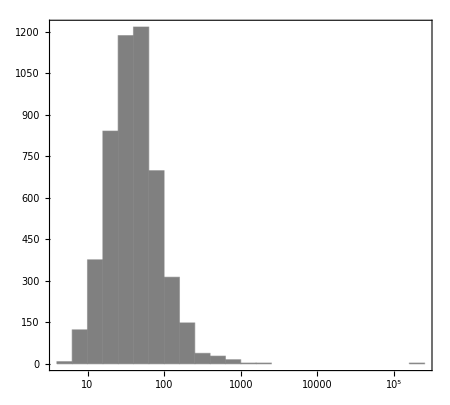

```mathematica
With[{sizes=#["ExplicitLength"]&/@Values[Values[Last/@association017a]]}, Histogram[sizes, "Log", PlotRange-> All, LabelStyle-> {Black,Large}, ImageSize-> 450,Frame-> True, ChartStyle-> Gray, AspectRatio->0.9]]
```

### Figure 3 D

```mathematica
testcase=Values[4706/.association017a]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[<68771>, {800, 800}],SparseArray[<92670>, {800, 800}],SparseArray[<121205>, {800, 800}],SparseArray[<160803>, {800, 800}]}

```mathematica
Export["testcase.mx", testcase]
```

testcase.mx

```mathematica
Length[testcase]
```

28

To generate the plot below, one must import the file “testcase.mx”

```mathematica
CellPlot[testcase[[-1]], {0, 800}]
```

-Graphics-

## Figure 4 B, E, (Spatial models, dividing cells sort to outside, Stream Plots)

```mathematica
systemB={c0'[t] == (2*P2[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P2[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

#### Figure 4B:

```mathematica
params10c={k->0.46, λ-> 22.5, σ-> 2.25, pbar-> 0.9, tend-> 200, δ-> 0.125};
```

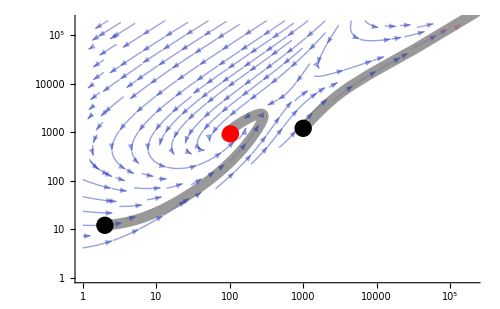

```mathematica
With[{system=systemB, c0init1=2, c1init1=10, c0init2=1000, c1init2=200,tmax=500, params=params10c},
Show[stream5c,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red, Point[Log@fp8c]}}]]
```

#### Figure 4E

```mathematica
params11d={k->0.51, λ-> 22.5, σ-> 2.25, pbar-> 0.9, tend-> 200, δ-> 0};
```

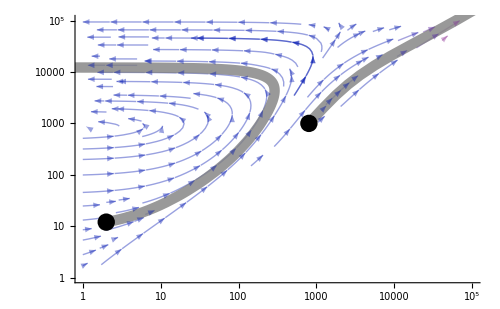

```mathematica
With[{system=systemB, c0init1=2, c1init1=10, c0init2=800, c1init2=200,tmax=50, params=params11d},
Show[stream6d,PP[system, c0init1,c1init1,10* tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] }}]]
```

## Figure 4 C, F, (Spatial models, dividing cells sort to outside, stochastic simulations)

#### For figure 4C

```mathematica
AbsoluteTiming[
stochSim5c=Flatten[Last@
Reap[
Do[Sow[TotalLast@NestWhileList[StepUpAsynchronousP2[#, params10c]&, {2,10}, 10^5>First[#]>0&&Last[#]<10^5&, 2, 100]], {100}]],1];]
```

{7267.82,Null}

this took 2 hours

```mathematica
Export["stochSim5c.mx",stochSim5c]
```

stochSim5c.mx

So 7% of cases escaped

```mathematica
escapers=Select[stochSim5c, Total[Last[#]]>10^4&];  Length[escapers]
```

7

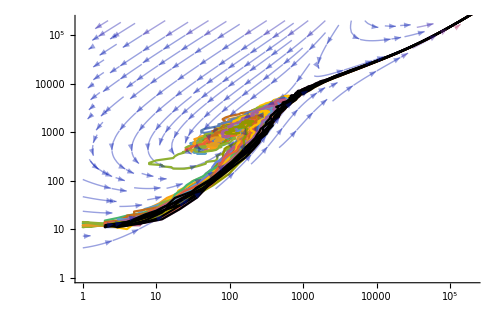

```mathematica
Show[stream5c,ListLogLogPlot[stochSim5c, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black] ]
```

#### For Figure 4F

```mathematica
params11d={k->0.51,λ->22.5,σ->2.25,pbar->0.9,tend->200,δ->0}
```

```mathematica
AbsoluteTiming[
stochSim6dAdditional2=Flatten[Last@
Reap[
Do[Sow[TotalLast@NestWhileList[StepUpAsynchronousP2[#, params11d]&, {2,2}, 10^5>First[#]>0&, 1, 300]], {100}]],1];]
```

{5928.79,Null}

```mathematica
Export["stochSim6dAdditional2.mx", stochSim6dAdditional2]
```

stochSim6dAdditional2.mx

```mathematica
escapers=Select[stochSim6dAdditional2, First[Last[#]]>1000&];Length[escapers]
```

8

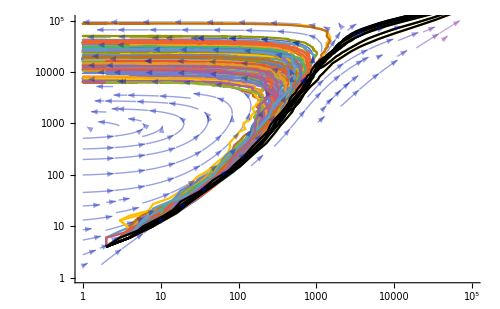

```mathematica
Show[stream6d,ListLogLogPlot[stochSim6dAdditional2, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

## Figure 4 H, K, (Spatial models, dividing cells sort to inside, Stream Plots)

```mathematica
systemC={c0'[t] == (2*P3[c0[t],c1[t],k,λ, σ, pbar]-1)c0[t],
c1'[t] == 2(1-P3[c0[t], c1[t],k,λ, σ, pbar])c0[t] -δ c1[t],
c0[0]==c0init, c1[0]==c1init};
```

```mathematica
systemC[[2]]/.n_'[t]-> 0/.P3[c0[t],c1[t],k,λ,σ,pbar]-> 1/2
```

0==c0[t]-δ c1[t]

#### For Figure 4H

```mathematica
params12d={k->0.459, λ-> 22.5, σ-> 2.5, pbar-> 0.9, tend-> 200, δ-> 0.1};
```

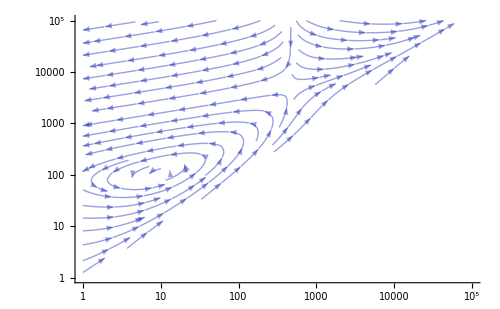

```mathematica
stream7d=With[{terms=Last/@systemCa/.n_[t]-> n},SP[terms, {c0,1,10^5},{s,1,10^5}, params12d]]
```

```mathematica
fp9d= FixedPointsN[systemC,params12d, 10,90]
```

{10.0885,110.973}

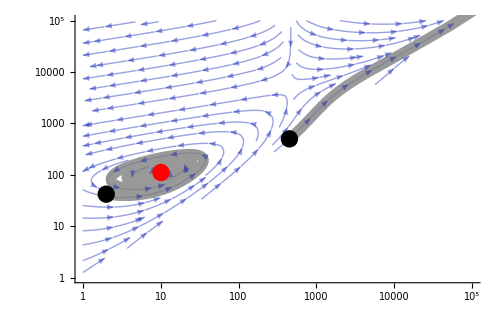

```mathematica
With[{system=systemC, c0init1=2, c1init1=40, c0init2=450, c1init2=50,tmax=500, params=params12d},
Show[stream7d,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red, Point[Log@fp9d]}}]]
```

#### For Figure 4K

```mathematica
params13b={k->0.52, λ-> 22.5, σ-> 2.5, pbar-> 0.9, tend-> 200, δ->0};
```

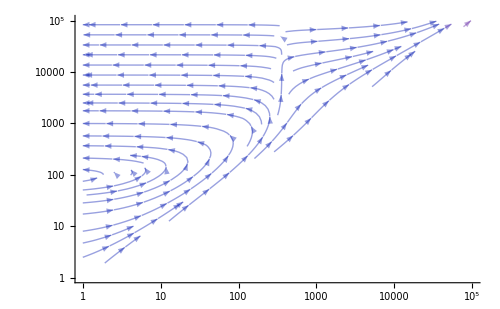

```mathematica
stream8b=With[{terms=Last/@systemCa/.n_[t]-> n},SP[terms, {c0,1,10^5},{s,1,10^5}, params13b]]
```

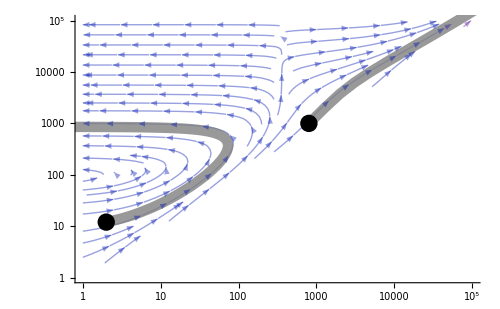

```mathematica
With[{system=systemC, c0init1=2, c1init1=10, c0init2=800, c1init2=200,tmax=50, params=params13b},
Show[stream8b,PP[system, c0init1,c1init1,10* tmax, params],PP[system, c0init2,c1init2, tmax, params],
Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] }}]]
```

## Figure 4 I, L, (Spatial models, dividing cells sort to inside, stochastic simulations)

```mathematica
IndividualStepUpP3[{c0_, c1_}, params_]:= 
With[{p=P3[c0, c1, k/.params, λ/.params, σ/.params, pbar/.params]},
{c0-1, c1}+RandomChoice[{p^2,(1-p)^2,2 (1-p) p}->{{2,0},{0,2},{1,1} }]- {0,RandomVariate[BinomialDistribution[c1,1-ⅇ^(-δ/c0) /.params]]}]
```

```mathematica
StepUpAsynchronousP3[{c0_, c1_}, params_]:= Nest[IndividualStepUpP3[#, params]&, {c0, c1}, c0]
```

#### For Figure 4I

This time we generate the list in steps so we can figure out how long simulation needs to take.  We initially stop trajectories when they reach 300 dividing cells so we can see how it’s working.  Then we continue them on.

```mathematica
params12b
```

{k→0.5,λ→22.5,σ→2.5,pbar→0.9,tend→200,δ→0.1}

```mathematica
Print@Now;
AbsoluteTiming[
stochSim10untotaled2=Flatten[Last@
Reap[
Do[Sow[NestWhileList[StepUpAsynchronousP3[#, params12b]&, {2,2}, 300>First[#]>0&, 1, 100]], {100}]],1];]
```

Tue 28 Jan 2025 13:45:19GMT-8

{313.971,Null}

Here we see that some trajectories look like they might be heading upward:

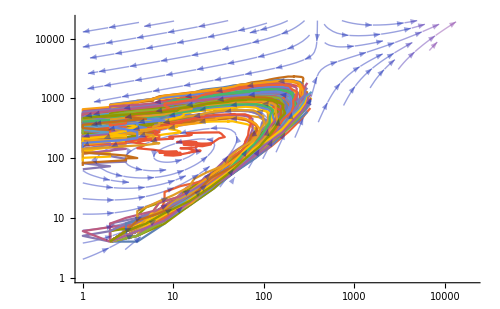

```mathematica
Show[stream7b,ListLogLogPlot[TotalLast/@stochSim10untotaled2, Joined-> True,AxesStyle->Thickness[0.0075], LabelStyle-> Large, ImageSize-> 500]]
```

Now we continue for an additional 40 cycles:

```mathematica
AbsoluteTiming[Do[Do[AppendTo[stochSim10untotaled2[[i]], 
Module[{endpoints=Last/@stochSim10untotaled2},
If[0<First[endpoints[[i]]]<10^5,StepUpAsynchronousP2[endpoints[[i]], params12d],endpoints[[i]] ]]], {i, Length[stochSim10untotaled2]}],40];]
```

{2836.25,Null}

Then we convert to {c0, s} rather than {c0, c1} form:

```mathematica
stochSim10 = TotalLast/@stochSim10untotaled2;
```

```mathematica
Export["stochSim10.mx",stochSim10]
```

stochSim10.mx

```mathematica
escapers=Select[stochSim10, First[Last[#]]>10^4&]; Length[escapers]
```

6

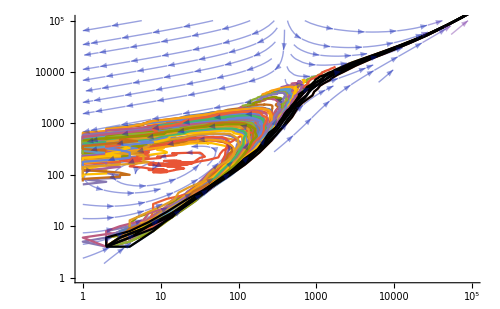

```mathematica
Show[stream7b,ListLogLogPlot[stochSim10, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

#### For Figure 4L

```mathematica
params13b={k->0.52, λ-> 22.5, σ-> 2.5, pbar-> 0.9, tend-> 200, δ->0};
```

```mathematica
Print@Now;
AbsoluteTiming[
stochSim11untotaledc=Flatten[Last@
Reap[
Do[Sow[NestWhileList[StepUpAsynchronousP3[#, params13b]&, {2,2}, 10^5>First[#]>0&, 1, 200]], {100}]],1];]
```

Thu 20 Mar 2025 09:35:43GMT-8

{2745.18,Null}

```mathematica
stochSim11c = TotalLast/@stochSim11untotaledc;
escapers = Select[stochSim11c, First[Last[#]]>10000&]; Length[escapers]
```

4

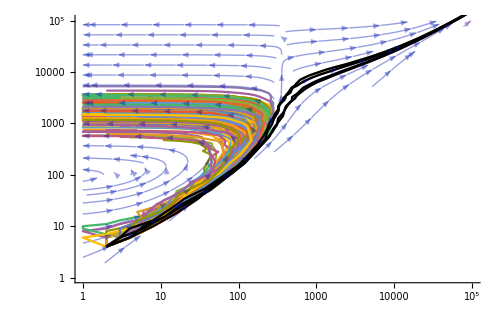

```mathematica
Show[stream8b,ListLogLogPlot[stochSim11c, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

## Figure 5 B, E, H (Mixed feedback models, stream plots)

In the first and second models (system 2) stem cells inhibit inhibition from terminal cells.  In the third model (system 4), terminal cells inhibit their own inhibition.

#### For Fig . 5B

```mathematica
params13 ={pbar->0.8,γ->0.006,ϕ->0.0022,n1->1,n2->1.5,d->0};
```

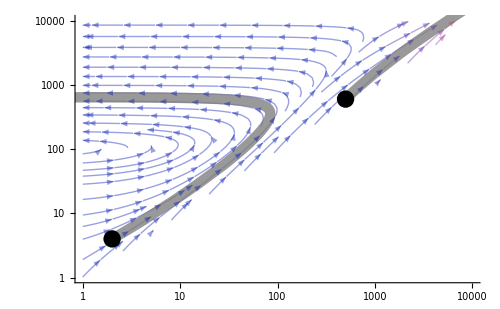

```mathematica
fig5b=With[{system=system2,c0init1=2, c1init1=2, c0init2=500, c1init2=100,tmax=500, params=params13},Show[stream9,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] }}]]
```

#### For Fig . 5E

```mathematica
params14 = {pbar-> 0.8, γ-> 0.006, ϕ-> 8.5 10^-4, n1-> 1, n2-> 1.5, d-> 0.4};
```

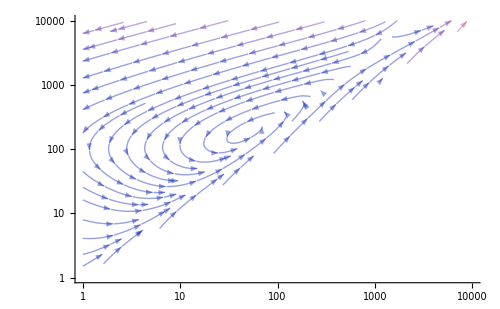

```mathematica
stream9a=With[{terms=Last/@system2a/.n_[t]-> n},SP[terms, {c0,1,10^4},{s,1,10^4}, params14]]
```

```mathematica
FixedPoints[system2, params14]
```

{{53.189,186.161},{778.434,2724.52}}

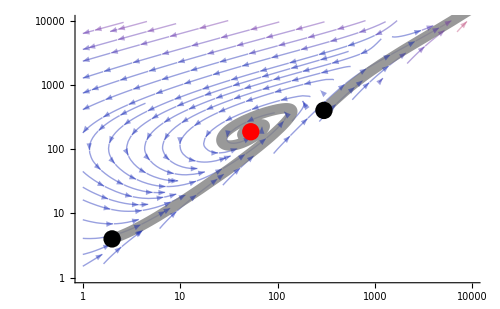

```mathematica
fig5e=With[{system=system2,c0init1=2, c1init1=2, c0init2=300, c1init2=100,tmax=500, params=params14},Show[stream9a,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red,Point[Log@{53.1889896862956,186.1614639020346}] }}]]
```

#### For Fig . 5H

```mathematica
params15 = {pbar-> 0.8, γ-> 0.004, ϕ-> 0.001, n1-> 1, n2-> 1.25, d-> 0.15};
```

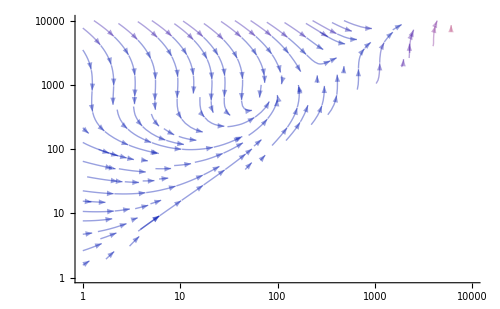

```mathematica
stream11=With[{terms=Last/@system4a/.n_[t]-> n},SP[terms, {c0,1,10^4},{s,1,10^4}, params15]]
```

```mathematica
FixedPoints[system4, params15]
```

{{81.7352,626.637},{164.552,1261.56}}

Figure 5H

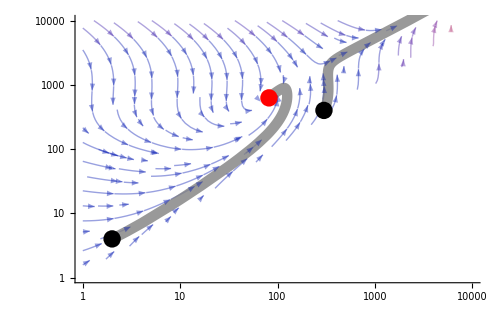

```mathematica
fig5h=With[{system=system4,c0init1=2, c1init1=2, c0init2=300, c1init2=100,tmax=500, params=params15},Show[stream11,PP[system, c0init1,c1init1, tmax, params],PP[system, c0init2,c1init2, tmax, params],Epilog-> {{PointSize[0.025],Black, Point[Log@{c0init1,c0init1+c1init1}], Point[Log@{c0init2,c0init2+c1init2}] },{PointSize[0.025],Red,Point[Log@{81.73519596666381,626.6365024110892}] }}]]
```

## Figure 5 C, F, I (Mixed feedback models, stochastic simulations)

#### Figure 5C

```mathematica
AbsoluteTiming[
stochSim7a=With[{params=params13},Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF[#1, #2,pbar/.params,n1/.params, n2/.params, γ/.params, ϕ/.params, d/.params]&,#]&, {1,0}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 200]], {100}]],1]];]
```

{9.04631,Null}

```mathematica
escapers=Select[stochSim7a, Last[Last[#]]>10^4&]; Length[escapers]
```

10

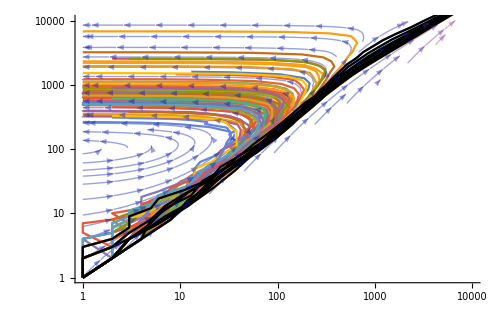

```mathematica
Show[stream9,ListLogLogPlot[stochSim7a, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

```mathematica
Export["stochSim7a.mx", stochSim7a]
```

stochSim7a.mx

#### Fig. 5F

```mathematica
AbsoluteTiming[
stochSim8=With[{params=params14},Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF[#1, #2,pbar/.params,n1/.params, n2/.params, γ/.params, ϕ/.params, d/.params]&,#]&, {1,0}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 100]], {100}]],1]];]
```

{22.2931,Null}

```mathematica
escapers=Select[stochSim8, Last[Last[#]]>10^4&]; Length[escapers]
```

3

```mathematica
Export["stochSim8.mx", stochSim8]
```

stochSim8.mx

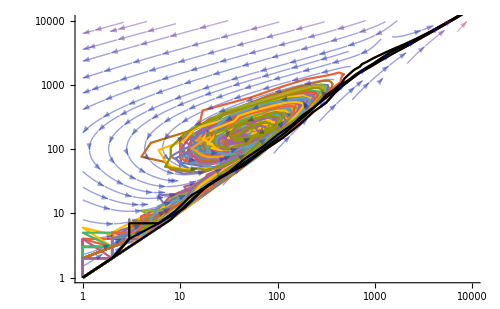

```mathematica
Show[stream9a,ListLogLogPlot[stochSim8, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

#### Fig. 5I

for the final case we need to switch from StepUpAsynchronousCF to StepUpAsynchronousCF2, because of the difference in the system:

```mathematica
AbsoluteTiming[
stochSim9=With[{params=params15},Flatten[Last@Reap[Do[Sow[TotalLast@NestWhileList[Apply[StepUpAsynchronousCF2[#1, #2,pbar/.params,n1/.params, n2/.params, γ/.params, ϕ/.params, d/.params]&,#]&, {1,0}, 10^4>First[#]>0&&Last[#]<10^4&, 2, 100]], {100}]],1]];]
```

{49.206,Null}

```mathematica
escapers=Select[stochSim9, Last[Last[#]]>10^4&]; Length[escapers]
```

6

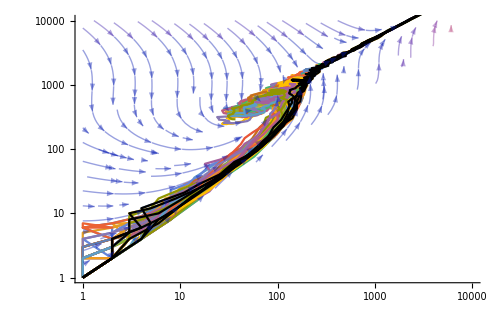

```mathematica
fig5i=Show[stream11,ListLogLogPlot[stochSim9, Joined-> True],ListLogLogPlot[escapers, Joined-> True, PlotStyle-> Black]]
```

```mathematica
Export["stochSim9.mx", stochSim9]
```

stochSim9.mx